```mathematica
<<Local`QFTToolKit2`
tuItalics
```

Tue 19 Nov 2019 08:59:32

```mathematica
tuGraphicDefs
```

```mathematica
$coordSolidAngle:={CG["Solid angle for sphere S^(n - 1)"],
{T[ω,"u",{1}]->Cos[T[θ,"d",{1}]],
T[ω,"u",{n_}]->xProduct[Sin[T[θ,"d",{j}]],{j,1,n-2}]Sin[T[θ,"d",{n-1}]],
{T[ω,"u",{i_}]->xProduct[Sin[T[θ,"d",{j}]],{j,1,i-1}]Cos[T[θ,"d",{i}]],{i,1,n-1}
},
{{0≤T[θ,"d",{i}]<π,1≤i<n-1},
0≤T[θ,"d",{n-1}]<2π
}
}[CG["define direction cosines"]],
$coordSolidAngleDiff={xSum[T[ω,"u",{i}]^2,{i,1,n}]->1,
d[Subscript[Ω, n_]]^2->xSum[d[T[ω,"u",{i}]]^2,{i,1,n+1}],
xSum[T[ω,"u",{i}]d[T[ω,"u",{i}]],{i,1,n}]->0
}[CG["$coordSolidAngleDiff ref: tuCoordSolidAngle[n_]"]],

{ tuSphereArea[d_]:=Subscript[S, d-1]->d π^(d/2)/Gamma[d/2+1];
tuSphereArea[4],
tuSphereVolume[d_]:=Subscript[V, d]->π^(d/2)/Gamma[d/2+1];
tuSphereVolume[4]
}[CG["definitions of Area and Volume of unit sphere in d-dimensions"]]

}[CG["$coordSolidAngle"]]

$coordSolidAngle

(**)
$geodesicEqn:=
{
tuDPartial[T[x,"u",{μ}],{λ,λ}]+T[Γ,"udd",{μ,ρ$,σ$}]tuDPartial[T[x,"u",{ρ$}],λ]tuDPartial[T[x,"u",{σ$}],λ]->0/.tuDExpandMultiVar,

tuChristoffel[g_]:=T[Γ,"udd",{i_,k_,l_}]->1/2 T[g,"uu",{i,m$}](tuDPartial[T[g,"dd",{m$,k}],l]+tuDPartial[T[g,"dd",{m$,l}],k]-tuDPartial[T[g,"dd",{k,l}],m$]),

(**)
tuGeodesicEqn::usage="tuGeodesicEqn[dsmetric_] compute the geodesic equations from the dsmetric_ in the form (d[s]^2→_).  This uses 'diffgeo.'(by M. Headrick, available at http://people.brandeis.edu/~headrick/Mathematica/) for computing Christoffel tensors and  returns a list of geodesic equations for each 'coord' where the symbol d[_] is used for proper time derivative. All other variables defined by 'diffgeo' are available after using this routine. *14Nov2018*";
(**)
tuGeodesicEqn[dsmetric_]:=Module[{$ds=dsmetric,$g,$d,$c},
$g=$ds//tuMetricProperTime;
coord=gvars/.$g;
metric=gmatrixdd/.$g;
<<diffgeo`diffgeo`;
$d=d/@coord;
$c=Christoffel;
$=Inner[Times,$c,$d,Plus,2];
d/@$d->-Inner[Times,$,$d,Plus,2]//Thread
];
}
```

{Solid angle for sphere S^(n - 1),{ω_1^1→Cos[θ_1^1],ω_n_^n_→Sin[θ_(-1+n)^(-1+n)] UnderBar[∏]_{j,1,-2+n}[Sin[θ_j^j]],{ω_i_^i_→Cos[θ_i^i] UnderBar[∏]_{j,1,-1+i}[Sin[θ_j^j]],{i,1,-1+n}},{{0≤θ_i^i<π,1≤i<-1+n},0≤θ_(-1+n)^(-1+n)<2 π}}[define direction cosines],{UnderBar[∑]_{i,1,n}[(ω_i^i)^2]→1,d[Ω_n_]^2→UnderBar[∑]_{i,1,1+n}[d[ω_i^i]^2],UnderBar[∑]_{i,1,n}[d[ω_i^i] ω_i^i]→0}[$coordSolidAngleDiff ref: tuCoordSolidAngle[n_]],{S_3→2 π^2,V_4→π^2/2}[definitions of Area and Volume of unit sphere in d-dimensions]}[$coordSolidAngle]

```mathematica
$metricSchwarzschild={
d[s]^2->-(1-2M G/r)d[t]^2+(1-2M G/r)^-1 d[r]^2+r^2(d[Ω]^2),{Subscript[r, s]->2 G M}[CG["Schwarzschild radius"]]}[CG["$metricSchwarzschild"]]
(*Rule for adding solid angle to Schwarzschild like metric*)
$s=$metricSchwarzschild;
$s=$s/.{d[t]->0,d[s]->0}//tuRule1//tuRuleSolveF[d[r]^2]//tuRule1;
$s[[2]]=-$s[[2]]+d[r]^2;
$coordSchwarzschildAddSolidAngle={$s}[CG["$coordSchwarzschildAddSolidAngle"]]

$metricMinkowski={
tuRule[$metricSchwarzschild]/.M->0}[CG["$metricMinkowski"]]

$metricNullCoordinateMinkowski=$={
{$uv={u->(t-r),v->(t+r)}}[CG["$uv null coordinates"]],
$tr=tuRuleSolve[$uv,{t,r}],
tuRule[$metricMinkowski][[1]]/.$tr//tudExpand[d,{}]//Simplify
};(ColumnForms[#1,2]&)[$][CG["$metricNullCoordinateMinkowski"]]

$metricPenrose=$={
$coordPenrose={v->Tan[ṽ],u->Tan[ũ],{ṽ,ũ}∈Interval[{-π/2,π/2}]}[CG["$coordPenrose"]],
tuRuleSolve[tuRule[$coordPenrose],{ṽ,ũ}]//Refine[#,C[1]==0&&C[2]==0]&,
($metricNullCoordinateMinkowski//tuRuleSelect[d[s]^2]//First)/.tuRule[$coordPenrose]//tudExpandvI[d]//Simplify
};(ColumnForms[#1,2]&)[$][CG["$metricPenrose"]]


$metricSchwarzschildKruskalSzekeres=$={$coordSchwarzschildKruskalSzekeres={{T->√Abs[r/(2M G)-1] Exp[r/(4M G)](Sinh[t/(4M G)]HeavisideTheta[r-2M G]+Cosh[t/(4M G)]HeavisideTheta[2M G-r]),X->√Abs[r/(2M G)-1] Exp[r/(4M G)](Cosh[t/(4M G)]HeavisideTheta[r-2M G]+Sinh[t/(4M G)]HeavisideTheta[2M G-r])}}[CG["$coordSchwarzschildKruskalSzekeres"]],
$00=$=$coordSchwarzschildKruskalSzekeres//tuRule;
$0=$s=$[[1;;2]];
$=T^2-X^2;
$=$->($/.$s)//Simplify;{$}[CG["Null geodesic at r→2MG"]],

$s2M=(r>2M G);
$=Inactive[Refine][$,$s2M],
$=$//Activate;
$sr=tuRuleSolve[$,{r}]//First,
$=Refine[$00,$s2M],
$=tuRuleSolve[$[[1]],{t}]//Refine[#,C[1]==0]&;
$=$/.$sr//FullSimplify;
{$sr,$//Last},
$=tuRule[$coordSchwarzschildKruskalSzekeres][[1;;2]]//Refine[#,$s2M]&;
$s=(d/@#)&/@$/.Abs[a_]->a//tudExpand[d,{M,G}];
$=$0=-d[T]^2+d[X]^2;
$=$0->($/.$s//Simplify);
$metricKrukalSzekeres=$={$,
$=Exp[-r/(2M G)]32 (M G)^3#/r&/@$//Collect[#,d[_],Simplify]&//Simplify,
$=r^2 d[Ω]^2+#&/@$;
$=d[s]^2->$[[1]]/.$sr//FullSimplify

};$[CG["$metricKrukalSzekeres"]],

$metricKrukalSzekeresNull=$={$s={T->(U+V)/2,X->-(U-V)/2},
$metricKrukalSzekeres/.$s//tudExpand[d]//FullSimplify,
$=$s//tuRuleSolveF[{U,V}];
$s=$coordSchwarzschildKruskalSzekeres//tuRuleSelect[T|X,HeavisideTheta];
$=$/.$s//TrigToExp//FullSimplify
};$[CG["$metricKrukalSzekeresNull"]]

};(ColumnForms[#1,4]&)[$][CG["$metricSchwarzschildKruskalSzekeres"]]


$einsteinEqn={T[R,"dd"][μ,ν]-T[g,"dd"][μ,ν]T[R,{},{}]/2+Λ T[g,"dd"][μ,ν]->8π G /c^4 T[T,"dd"][μ,ν]}[CG["$einsteinEqn"]]
```

{d[s]^2→d[r]^2/(1-(2 G M)/r)+(-1+(2 G M)/r) d[t]^2+r^2 d[Ω]^2,{r_s→2 G M}[Schwarzschild radius]}[$metricSchwarzschild]

{d[r]^2→d[r]^2-(2 G M-r) r d[Ω]^2}[$coordSchwarzschildAddSolidAngle]

{{d[s]^2→d[r]^2-d[t]^2+r^2 d[Ω]^2,r_s→0}}[$metricMinkowski]

{{u→-r+t,v→r+t}}[$uv null coordinates]
t→(u+v)/2
r→1/2 (-u+v)
d[s]^2→1/4 (-4 d[u] d[v]+(u-v)^2 d[Ω]^2)[$metricNullCoordinateMinkowski]

{v→Tan[ṽ],u→Tan[ũ],{ṽ,ũ}∈Interval[{-π/2,π/2}]}[$coordPenrose]
ṽ→ArcTan[v]
ũ→ArcTan[u]
d[s]^2→-1/4 Sec[ũ]^2 Sec[ṽ]^2 (4 d[ũ] d[ṽ]-d[Ω]^2 Sin[ũ-ṽ]^2)[$metricPenrose]

T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)])
X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)])[$coordSchwarzschildKruskalSzekeres]
T^2-X^2→ⅇ^(r/(2 G M)) Abs[1-r/(2 G M)] (HeavisideTheta[2 G M-r]^2-HeavisideTheta[-2 G M+r]^2)[Null geodesic at r→2MG]
Refine[T^2-X^2→ⅇ^(r/(2 G M)) Abs[1-r/(2 G M)] (HeavisideTheta[2 G M-r]^2-HeavisideTheta[-2 G M+r]^2),r>2 G M]
r→2 (G M+G M ProductLog[(T^2-X^2)/ⅇ])
T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] Sinh[t/(4 G M)]
X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] Cosh[t/(4 G M)]
r→2 (G M+G M ProductLog[(T^2-X^2)/ⅇ])
t→4 G M ArcSinh[(ⅇ^(1/2 (-1-ProductLog[((T-X) (T+X))/ⅇ])) T)/(√Abs[ProductLog[((T-X) (T+X))/ⅇ]])]
-d[T]^2+d[X]^2→(ⅇ^(r/(2 G M)) (-r^2 d[r]^2+(-2 G M+r)^2 d[t]^2))/(32 G^3 M^3 (2 G M-r))
-(32 ⅇ^(-r/(2 G M)) G^3 M^3 (d[T]^2-d[X]^2))/r→-(r d[r]^2)/(2 G M-r)+(-1+(2 G M)/r) d[t]^2
d[s]^2→(4 G^2 M^2 (-4 d[T]^2+4 d[X]^2+ⅇ^(1+ProductLog[((T-X) (T+X))/ⅇ]) d[Ω]^2 (1+ProductLog[((T-X) (T+X))/ⅇ])^3))/(ⅇ^(1+ProductLog[((T-X) (T+X))/ⅇ])+T^2-X^2)[$metricKrukalSzekeres]
T→(U+V)/2
X→1/2 (-U+V)
-d[U] d[V]→(ⅇ^(r/(2 G M)) (-r^2 d[r]^2+(-2 G M+r)^2 d[t]^2))/(32 G^3 M^3 (2 G M-r))
-(32 ⅇ^(-r/(2 G M)) G^3 M^3 d[U] d[V])/r→-(r d[r]^2)/(2 G M-r)+((2 G M-r) d[t]^2)/r
d[s]^2→(4 G^2 M^2 (-4 d[U] d[V]+ⅇ^(1+ProductLog[(U V)/ⅇ]) d[Ω]^2 (1+ProductLog[(U V)/ⅇ])^3))/(ⅇ^(1+ProductLog[(U V)/ⅇ])+U V)
U→ⅇ^((r-t)/(4 G M)) √Abs[1-r/(2 G M)] (HeavisideTheta[2 G M-r]-HeavisideTheta[-2 G M+r])
V→ⅇ^((r+t)/(4 G M)) √Abs[1-r/(2 G M)] (HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r])[$metricKrukalSzekeresNull][$metricSchwarzschildKruskalSzekeres]

{Λ g_μν^μν-1/2 g_μν^μν R_^+R_μν^μν→(8 G π T_μν^μν)/c^4}[$einsteinEqn]

```mathematica
$metricEddingtonFinkelstein=$={$=$coordEddingtonFinkelstein={{v->t+SuperStar[r][CG["tortoise coordinate"]]}[CG["ingoing null ray"]],
{u->t-SuperStar[r][CG["tortoise coordinate"]]}[CG["outgoing null ray"]]
};
AppendTo[$coordEddingtonFinkelstein,$//tuRuleSolveF[{t,SuperStar[r]}]],
$coordTortoise=
{$=SuperStar[r][CG["tortoise coordinate"]]->r+2 G M Log[Abs[r/(2 G M)-1]],
$sr=tuOpIndependentVar[tuRuleSolve,op$[$,r]]//tuRule//First,
$sr1=$sr//tuRuleSolveF[ProductLog[_]]//FullSimplify//First,
$sr2=$sr//tuRuleSolveF[SuperStar[r]]//First
},
{
$=$metricSchwarzschild//tuRule1;
$=$/.$sr//tudExpandvI[d,{G, M}]//FullSimplify;
$=$/.$sr1//Collect[#,d[_],Simplify]&,
$s=$coordEddingtonFinkelstein//tuRuleSolveF[{t,SuperStar[r]}];
$=$/.$s//tudExpandvI[d,{G,M}]//Collect[#,d[_]]&
},

{$s=$coordEddingtonFinkelstein//tuRuleSelect[v]//tuRuleSolveF[SuperStar[r]]//First,
$srv=$sr/.$s,
$=$metricSchwarzschild//tuRule//First;
$=$/.$srv//tuOpIndependentVar[tudExpand,op$[d,{M,G}][#]]&//FullSimplify//Collect[#,d[_],FullSimplify]&;
$=$/.tuRuleSolve[$s,t]/.Exp[a_]:>Exp[Expand[a]]/.$sr1/.$sr2;
$metricEddingtonFinkelsteinIn=$dsv=$=$//tuOpIndependentVar[tudExpand,op$[d,{M,G}][#]]&//Simplify;{$}[CG["$metricEddingtonFinkelsteinIn"]]//Framed
},

{$s=$coordEddingtonFinkelstein//tuRuleSelect[u]//tuRuleSolveF[SuperStar[r]]//First,
$srv=$sr/.$s,
$=$metricSchwarzschild//tuRule//First;
$=$/.$srv//tuOpIndependentVar[tudExpand,op$[d,{M,G}][#]]&//FullSimplify//Collect[#,d[_],FullSimplify]&;
$=$/.tuRuleSolve[$s,t]/.Exp[a_]:>Exp[Expand[a]]/.$sr1/.$sr2;
$metricEddingtonFinkelsteinOut=$dsu=$=$//tuOpIndependentVar[tudExpand,op$[d,{M,G}][#]]&//Simplify;{$}[CG["$metricEddingtonFinkelsteinOut"]]//Framed
}

};
{(ColumnForms[#1,2]&)[$]}[CG["$metricEddingtonFinkelstein"]]
```

{{v→t+r^*[tortoise coordinate]}[ingoing null ray]
{u→t-r^*[tortoise coordinate]}[outgoing null ray]
{t→(u+v)/2,r^*→1/2 (-u+v)}
r^*[tortoise coordinate]→r+2 G M Log[Abs[-1+r/(2 G M)]]
r→2 (G M+G M ProductLog[ⅇ^(-1+r^*/(2 G M))])
ProductLog[ⅇ^(-1+r^*/(2 G M))]→-1+r/(2 G M)
r^*→2 (G M+G M Log[(ⅇ^(-1+r/(2 G M)) (-2 G M+r))/(2 G M)])
{d[s]^2→(-1+(2 G M)/r) d[t]^2+r^2 d[Ω]^2+(1-(2 G M)/r) d[r^*]^2,r_s→2 G M}
{d[s]^2→(-1+(2 G M)/r) d[u] d[v]+r^2 d[Ω]^2,r_s→2 G M}
r^*→-t+v
r→2 (G M+G M ProductLog[ⅇ^(-1+(-t+v)/(2 G M))])
{d[s]^2→2 d[r] d[v]+(-1+(2 G M)/r) d[v]^2+r^2 d[Ω]^2}[$metricEddingtonFinkelsteinIn]
r^*→t-u
r→2 (G M+G M ProductLog[ⅇ^(-1+(t-u)/(2 G M))])
{d[s]^2→-2 d[r] d[u]+(-1+(2 G M)/r) d[u]^2+r^2 d[Ω]^2}[$metricEddingtonFinkelsteinOut]}[$metricEddingtonFinkelstein]

Penrose diagram of Minkowski space(clockwise rotated 45^o from traditional plot)
→ {u,v}→{-r+t,r+t}
→ {ṽ,ũ}→{ArcTan[v],ArcTan[u]}
→ {ṽ,ũ}→{ArcTan[r+t],-ArcTan[r-t]}
→ {-π/2,π/2}
→ {ArcTan[r+t],-ArcTan[r-t]}{r→4,r→1,r→0.3,r→0,r→-0.3,r→-1,r→-4,r→ũ,r→ṽ}{r -> 4,r -> 1,r -> 0.3,r -> 0,r -> -0.3,r -> -1,r -> -4,     ~
r -> u,     ~
r -> v}

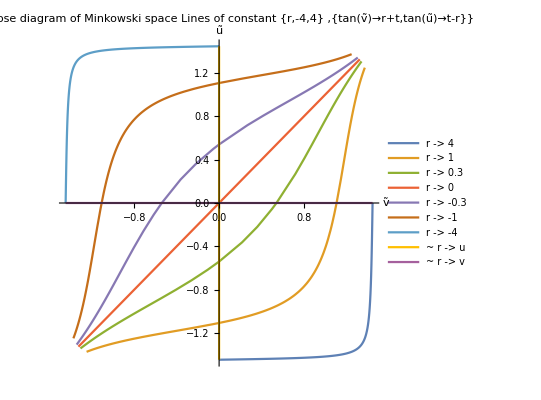

```mathematica
PR["Penrose diagram of Minkowski space(clockwise rotated 45^o from traditional plot)",
$metricNullCoordinateMinkowski;
$=$0={u,v};
Yield,$=$0->($/.tuRule[$metricNullCoordinateMinkowski]),
$metricPenrose;
$=$1={ṽ,ũ};
Yield,$=$1->($1/.tuRule[$metricPenrose]),

$[[2]]=$[[2]]/.tuRule[$metricNullCoordinateMinkowski];
Yield,$2=$,
Yield,$[[2]]=$[[2]]/.t->0//Limit[#,r->-∞]&,
Yield,$=$2[[2]],
$t=Table[$/.r->ii,{ii,Flatten[{Reverse[$ii={.3,1,4}],0,-$ii,-t,t}]}]//Flatten[#,0]&;
$legend=Table[r->ii,{ii,Flatten[{Reverse[$ii={.3,1,4}],0,-$ii,-t,t}]}]/.{-t->ũ,t->ṽ},
$legend=ToString/@($legend)
];
$plotMinkowskiPenrose=ParametricPlot[$t,{t,-4,4},AxesLabel->$1,PlotLegends->$legend,PlotLabel->{"Penrose diagram of Minkowski space\nLines of constant {r,-4,4}\n",Tan/@#&/@$2//Thread}]
```

Plot of Schwarzschild solution: $metricSchwarzschildKruskalSzekeres
$coordSchwarzschildKruskalSzekeres T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)])
X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)])
For {M→1,G→1} and r: {4 M,10 M,1.9 M,0.00001 M}
→ {X,T}

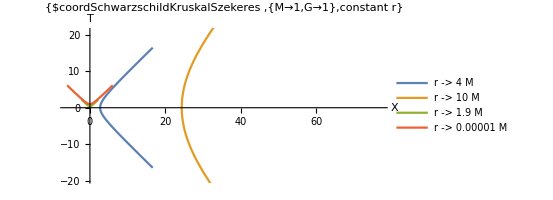

```mathematica
PR["Plot of Schwarzschild solution: $metricSchwarzschildKruskalSzekeres",
NL,"$coordSchwarzschildKruskalSzekeres ",$0=tuRule[$coordSchwarzschildKruskalSzekeres];(ColumnForms[#1,2]&)[$0],
$sM={M->1,G->1};
NL,"For ",$sM," and r: ",$rs=Table[r,{r,M{4,10,1.9,.00001}}],
Yield,$label=$00={X,T},
$t=Table[$label/.($0),{r,$rs}]/.$sM;
$legend=ToString/@Thread[r->$rs];
$plotSchwarzschildKruskalSzekeres=ParametricPlot[$t,{t,-10,10},AxesLabel->$label,PlotLegends->$legend,PlotLabel->{"$coordSchwarzschildKruskalSzekeres\n",$sM,"constant r"}];""
]
$plotSchwarzschildKruskalSzekeres
```

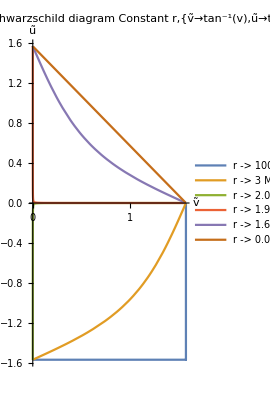
Penrose diagram for $metricSchwarzschildKruskalSzekeres
$coordSchwarzschildKruskalSzekeres T→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[2 G M-r]+HeavisideTheta[-2 G M+r] Sinh[t/(4 G M)])
X→ⅇ^(r/(4 G M)) √Abs[-1+r/(2 G M)] (Cosh[t/(4 G M)] HeavisideTheta[-2 G M+r]+HeavisideTheta[2 G M-r] Sinh[t/(4 G M)]){u→T-X,v→T+X} and {ṽ→ArcTan[v],ũ→ArcTan[u]}
For {M→1,G→1}
This is Penrose-Carter diagram of the Schwarzschild solution clockwise rotated by 45^o. The ṽ<0 region are not shown. The lines -Graphics-
{r -> 100 M, close to r→∞, ℐ^±,𝒾^*}
{r -> 2.0001 M, close to r→2M, ũ|ṽ→0}
{r -> 0.00001 M, close to r→0, singularity}$plotPenroseKruskalSzekeres

```mathematica
PR["Penrose diagram for $metricSchwarzschildKruskalSzekeres",
NL,"$coordSchwarzschildKruskalSzekeres ",$0=tuRule[$coordSchwarzschildKruskalSzekeres];(ColumnForms[#1,2]&)[$0],
$label={ṽ,ũ};
$suv={u->T-X,v->T+X},and,
$luv=$=tuRuleSelect[$label][$metricPenrose],
$=MapAt[#/.$suv&,#,2]&/@$;
$1=$/.$0;
NL,"For ",$sM,
$rs=Table[r,{r,M{100,3,2.0001,1.9999,1.6,.00001}}];
$t=Table[$label/.($1),{r,$rs}]/.$sM;
$legend=ToString/@Thread[r->$rs];
$plotPenroseKruskalSzekeres=ParametricPlot[$t,{t,-100,100},AxesLabel->$label,PlotLegends->$legend,PlotLabel->{"Penrose-Carter-Schwarzschild diagram\nConstant r",$luv}];
$metricPenroseSchwarzschildKruskalSzekeres={$metricPenrose,$suv,$0,$1};
NL,"This is Penrose-Carter diagram of the Schwarzschild solution clockwise rotated by 45^o. The ṽ<0 region are not shown. The lines ",
$={{$legend[[1]]," close to r→∞, ℐ^±,𝒾^*"},
{$legend[[3]]," close to r→2M, ũ|ṽ→0"},
{$legend[[-1]]," close to r→0, singularity"}
};(ColumnForms[#1,2]&)[$];
$=$plotPenroseKruskalSzekeres={$plotPenroseKruskalSzekeres,$};(ColumnForms[#1,2]&)[$],CG["$plotPenroseKruskalSzekeres"]
];
```

Extended conformal Schwarzschild spacetime{T[-π/2,π/2],X[-π/2,π/2]} $plotPenroseKruskalSzekeres diagram centered on M Fig.12.2.
Compare with $plotPenroseKruskalSzekeres which shows the region ṽ>0

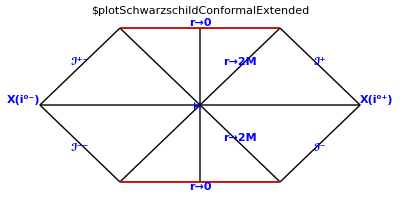

```mathematica
PR["Extended conformal Schwarzschild spacetime{T[-π/2,π/2],X[-π/2,π/2]} $plotPenroseKruskalSzekeres diagram centered on M Fig.12.2.
Compare with $plotPenroseKruskalSzekeres which shows the region ṽ>0"];

$plotSchwarzschildConformalExtended:={$pt={Range[-3,3],Range[-3,3]}//Tuples;
$offset=.3;
tuGraphicDefs;
Graphics[MapIndexed[Text[#2,#1]&,$pt]];

$line={{mid[34,40],$pt[[46]]},
{mid[30,38],$pt[[46]]},

{$pt[[25]],mid[26,27]},
{mid[23,24],$pt[[25]]},

{mid[10,16],$pt[[25]]},
{mid[12,20],mid[34,40]},

{mid[10,16],mid[30,38]},
{$pt[[25]],mid[30,38]},

{mid[12,20],$pt[[25]]},
{$pt[[25]],mid[34,40]},

{$pt[[4]],$pt[[25]]},
{$pt[[25]],$pt[[46]]},
{$pt[[4]],mid[12,20]},
{$pt[[4]],mid[10,16]}

};

Graphics[{Thin,Black,Map[Line[#]&,$line],
Thick,Red,Line[$line[[6]]],Line[$line[[7]]],
Blue,(*
MapIndexed[Text[#2,(#1[[1]]+#1[[2]])/2]&,$line],*)

Text[Style[T,Bold,Medium],$pt[[25]],{0,-$offset},{0,1}],
Text[Style[X[ii^("0+")],Bold,Medium],$pt[[46]],{-4 $offset,-2 $offset}],
Text[Style[X[ii^("0-")],Bold,Medium],$pt[[4]],{4 $offset,-2 $offset}],

Text[Style["ℐ^-",Bold,Medium],midline[2],{ $offset,2 $offset},{1,1}],
Text[Style["ℐ^(--)",Bold,Medium],midline[14],{ $offset,2 $offset},{1,-1}],

Text[Style["ℐ^+",Bold,Medium],midline[1],{$offset,-3 $offset},{1,-1}],
Text[Style["ℐ^(+-)",Bold,Medium],midline[13],{$offset,-3 $offset},{1,1}],
Text[Style["r→0",Bold,Medium],midline[6],{$offset,-3 $offset},{1,0}],
Text[Style["r→0",Bold,Medium],midline[7],{$offset,3 $offset},{1,0}],
Text[Style["r→2M",Bold,Medium],midline[10],{$offset,-3 $offset},{1,1}],
Text[Style["r→2M",Bold,Medium],midline[8],{$offset,-3 $offset},{1,-1}]
},PlotLabel->"$plotSchwarzschildConformalExtended"
]
}
$plotSchwarzschildConformalExtended
```

```mathematica
$=$metricRindler={d[s]^2->-ρ^2 d[σ]^2+d[ρ]^2,ρ->1/a,σ->a τ[CG["observer's proper time"]],
{r->ρ Cosh[σ],t->ρ Sinh[σ]
}[CG["Minkowski relationship"]]}[CG["Rindler metric"]];
(ColumnForms[#1,2]&)[$]
```

d[s]^2→d[ρ]^2-ρ^2 d[σ]^2
ρ→1/a
σ→a τ[observer's proper time]
{r→ρ Cosh[σ],t→ρ Sinh[σ]}[Minkowski relationship][Rindler metric]

```mathematica
"Ref:"-> URL["https://en.wikipedia.org/wiki/De_Sitter–Schwarzschild_metric"]

$metricSchwarzschildDeSitter=$={
d[s]^2->-f[r] d[t]^2+d[r]^2/f[r]+r^2 d[Ω]^2,
{{f[r]->1-2a[M[CG["BH mass"]]]/r}[CG["Schwarzschild black hole space"]],
{f[r]->1-b[Λ[CG["cosmological constant"]]] r^2}[CG["deSitter space"]],
{f[r]->1-2a[M]/r-b[Λ] r^2}[CG["SchwarzschildDeSitter space"]]

}[CG["from vacuum Einstein equations"]],
{d[s]^2->-(1-2M G/r-Λ r^2/3)d[t]^2+(1-2M G/r-Λ r^2/3)^-1 d[r]^2+r^2(d[Ω]^2)}[CG["typical form"]]

}[CG["$metricSchwarzschildDeSitter"]];
(ColumnForms[#1,4]&)[$]
```

Ref:→URL[https://en.wikipedia.org/wiki/De_Sitter–Schwarzschild_metric]

d[s]^2→r^2 d[Ω]^2+d[r]^2/f[r]-d[t]^2 f[r]
{f[r]→1-(2 a[M[BH mass]])/r}[Schwarzschild black hole space]
{f[r]→1-r^2 b[Λ[cosmological constant]]}[deSitter space]
{f[r]→1-(2 a[M])/r-r^2 b[Λ]}[SchwarzschildDeSitter space][from vacuum Einstein equations]
d[s]^2→d[r]^2/(1-(2 G M)/r-(r^2 Λ)/3)+(-1+(2 G M)/r+(r^2 Λ)/3) d[t]^2+r^2 d[Ω]^2[typical form][$metricSchwarzschildDeSitter]

```mathematica
$metricReissnerNordstrom={$={$={d[s]^2->-h d[t]^2+h^-1 d[r]^2+r^2 d[Subscript[Ω, iD-2]]^2,h->1-2μ[CG["mass parameter"]]/r^(iD-3)+θ[CG["charge parameter"]]^2/r^(2(iD-3)),
M->μ(iD-2)Subscript[S, iD-2]/(8π G),
{Q^2->(iD-2)(iD-3)Subscript[S, iD-2]/(8π G)θ^2}[CG["electric charge"]],
tuSphereArea[iD-1]
},
$=tuRuleEliminate[{μ,θ^2,Subscript[S, _]}][$];
$[[1]]/.$[[2]]//Simplify
}}[CG["$metricReissnerNordstrom in iD-dim (M. Ammon, J Erdmenger, 'Gauge/Gravity Duality', p.85)"]]
```

{{{d[s]^2→d[r]^2/h-h d[t]^2+r^2 d[Ω_(-2+D)]^2,h→1+r^(-2 (-3+D)) θ[charge parameter]^2-2 r^(3-D) μ[mass parameter],M→(μ (-2+D) S_(-2+D))/(8 G π),{Q^2→(θ^2 (-3+D) (-2+D) S_(-2+D))/(8 G π)}[electric charge],S_(-2+D)→(π^(1/2 (-1+D)) (-1+D))/Gamma[1+1/2 (-1+D)]},d[s]^2→r^2 d[Ω_(-2+D)]^2+d[r]^2/(1-(8 G π^(3/2-D/2) r^(3-2 D) Gamma[(1+D)/2] (-Q^2 r^3-6 M r^D+2 M r^D D))/((-3+D) (-2+D) (-1+D)))-d[t]^2 (1-(8 G π^(3/2-D/2) r^(3-2 D) Gamma[(1+D)/2] (-Q^2 r^3-6 M r^D+2 M r^D D))/((-3+D) (-2+D) (-1+D)))}}[$metricReissnerNordstrom in iD-dim (M. Ammon, J Erdmenger, 'Gauge/Gravity Duality', p.85)]

```mathematica
tuSaveAllVariables[]
```